{{0,0.35},{1,0.245},{2,0.1715},{3,0.12005},{4,0.084035},{5,0.0588245},{6,0.0411771},{7,0.028824},{8,0.0201768},{9,0.0141238}}

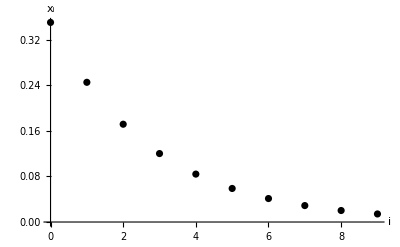

/home/parada/college/fc/Projeto1/data.pdf

```mathematica
dados = Import["/home/parada/college/fc/Projeto1/data.txt","Table"]

fig = ListPlot[dados, AxesLabel->{"i","x_i"}, PlotStyle->Black]

Export["/home/parada/college/fc/Projeto1/data.pdf", fig,"PDF"]
```